```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"]
```

/Users/pjoot/project/figures/blogit

```mathematica
<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→16,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

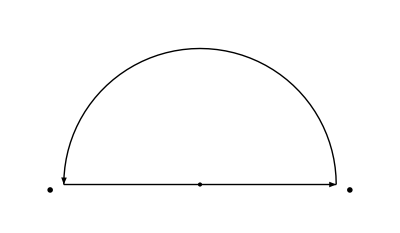

```mathematica
ClearAll[R, lineArrow, xrange, semicircleArrow, fourPolesFig1]
R=5; 
xrange = {{-R,0},{R,0}};
lineArrow=Graphics[{
Thick,Arrow[xrange],
Text[MaTeX["-R"], {-1.1 R, -0.2}],
Text[MaTeX["R"], {1.1 R, -0.2}],
PointSize -> Large,
Point[{0,0}]
}];

(*Semicircular arc with arrow*)
semicircleArrow=Graphics[{Thick,Arrow[Table[{R Cos[t],R Sin[t]},{t,0,Pi,Pi/50}]]}];

fourPolesFig1 = Show[lineArrow,semicircleArrow,AspectRatio->Automatic,PlotRange->{{-R-1,R+1},{-1,R+1}},Axes->False,(*Remove axes*)Ticks->None,(*Remove ticks*)Frame->False (*No frame*)]
```

```mathematica
peeters`exportForLatex["fourPolesFig1",fourPolesFig1]
```

{fourPolesFig1.eps,fourPolesFig1pn.png}

```mathematica
Integrate[1/(x^4 + 1), {x, 0, Infinity}]
```

π/(2 √2)

```mathematica
r2 = Sqrt[2]
(z - (1+I)/r2)(z - (-1+I)/r2)((z + I/r2)^2 - 1/2) // Expand
```

√2

1+z^4

```mathematica
(2 I + 1)^2 - 1 - ((2I -1)^2 - 1)
```

8 ⅈ